# chip-trap adiabatic potentials for NASA/CAL

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}

If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
Get["BatesConstants.m"]
Get["SMThreeBiasCoilsModel.m"]
Get["SMThreeChipModel.m"]
Get["SMThreeTraps.m"]
Get["RbGroundStateAlgebra.m"]
```

ℏ::shdw: Symbol ℏ appears in multiple contexts {RbGroundStateAlgebra`,Global`}; definitions in context RbGroundStateAlgebra` may shadow or be shadowed by other definitions.

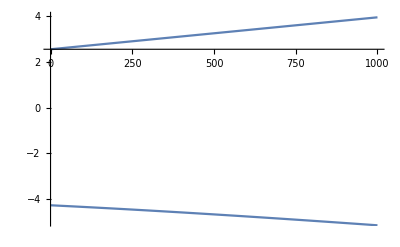

```mathematica
Show[{
Plot[ZeemanShiftF2[b*Gauss][[5]]/10^9,{b,0,1000}],
Plot[ZeemanShiftF1[b*Gauss][[3]]/10^9,{b,0,1000}]
},
PlotRange->{-5,4}]
```

## magnetic field from the chip (ii)

```mathematica
(* REDEFINITION OF CHIP PARAMETERS MUST HAPPEN HERE *)
```

```mathematica
tableTest=tableZHaB6;
minimizationSearchRegion={{-0.4 mm, 0.4mm},{0.5mm,2.4mm},{1mm,20μm}};
```

```mathematica
BChipMag[x_, y_, z_] :=(ChipTrapABField[x, y, z, #1, #2,#3, #4, #5, #6, #7, #8]&@@convertCALTableToTrapParameters@tableTest) Gauss;  
BChipMagC=Compile[{x,y,z},Evaluate[BChipMag[x,y,z]]]; 
BChipMagC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=BChipMagC[x,y,z];
 
BChip[x_, y_, z_] :=   (ChipTrapABVecField[x, y, z, #1, #2,#3, #4, #5, #6, #7, #8]&@@convertCALTableToTrapParameters@tableTest) Gauss;
BChipDirection[x_, y_, z_] := BChip[x, y, z]/BChipMag[x, y, z]
BChipDirectionC=Compile[{x,y,z},Evaluate@BChipDirection[x,y,z]];
BChipDirectionC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=BChipDirectionC[x,y,z];

BChipMagC=Compile[{x,y,z},Evaluate[BChipMag[x,y,z]]];
BChipMagC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=BChipMagC[x,y,z];
printTableValues@tableTest;

{x1,y1,z1}=Chop@(z0AB[#1,#2,#3,#4,#5,#6,#7,#8,minimizationRegion->minimizationSearchRegion]&@@convertCALTableToTrapParameters@tableTest);
Print["x1 = ", Round[1000000 (x /. x1),.1], " μm"]
Print["y1 = ", Round[1000000 (y /. y1),.1], " μm"]
Print["z1 = ", Round[1000000 (z /. z1),.1], " μm"]
x1=x1[[2]];
y1=y1[[2]];
z1=z1[[2]];
Bmin1=BChipMag[x1,y1,z1]/Gauss;(* Magnitude of the field at the minimum in Gauss *)
B0 = BChipMag[x1,y1,z1]; (* As far as I can tell, the same as Bmin1*Gauss, so B0 is in Tesla *)
```

AZ1_sel | AZ2_sel | AZ1 | AZ2 | H1&H2 | T1 | T2 | Y | Z
0 | 2 | -0.8643 | 0. | 0.36 | 0.00443 | 0.00443 | 0.07 | -0.1235

x1 = -16.7 μm

y1 = 1045.3 μm

z1 = 729.5 μm

Bmin = 3.52 G

trap bottom = 2.463 MHz

Depth = 1.57 G

frequencies: {{ϕ,159,θ,85},{ϕ,-93,θ,17},{ϕ,-112,θ,106},{17.,23.06,28.18}} Hz

Aspect Ratio = 1.66

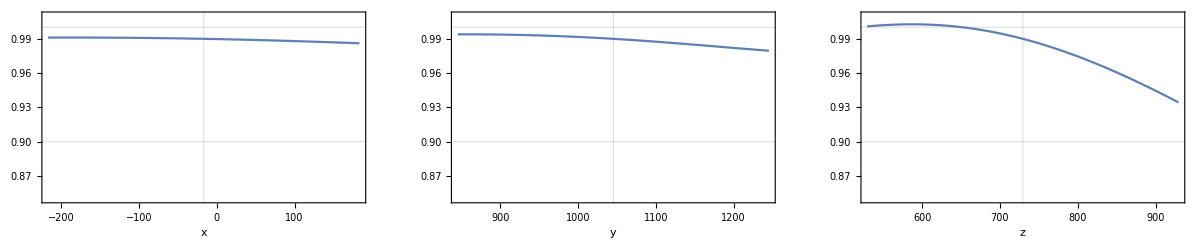

0.255855

0.792841

3.48579

```mathematica
ClearAll[XCosineAccurate,XCosineAccurateC,XCosineAccurateC2]
XCosineAccurate[x_,y_,z_]:=Sin[ArcCos[Dot[BChipDirection[x,y,z],mwUnitVec[x,y,z]]]];  (* projection between local field and ideally-orthogonal rf polarization, cf. p. 89 of notes. *)
GermanAngle[x_,y_,z_]:=ArcCos[Dot[BChipDirectionC2[x,y,z],mwUnitVecC2[x,y,z]]];  (* projection between local field and ideally-orthogonal rf polarization *)
XCosineAccurateC=Compile[{x,y,z},Evaluate[XCosineAccurate[x,y,z]]];
XCosineAccurateC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:= XCosineAccurateC[x,y,z];

Print["Bmin = ", NumberForm[Bmin1,3], " G"]
Print["trap bottom = "  ,Δguess = ((ZeemanShift[B0]//Differences //Mean)/1*^3 //Round)/1000.," MHz"]
Depth1=BChipMagC2[x1,y1,1.0]/Gauss-Bmin1; (*The comparison field is evaluated at z=1.0 is 1 m, essentially infinity.*)
Print["Depth = ", NumberForm[Depth1,3], " G"]
freqs1=
(ChipTrapABFrequencies[#1,#2,#3,#4,#5,#6,#7,#8,specifiedPosition->{x1,y1,z1}]&@@convertCALTableToTrapParameters@tableTest);
Print["frequencies: ", NumberForm[freqs1,4], " Hz"]
Print["Aspect Ratio = ", NumberForm[Max[freqs1[[4]]]/Min[freqs1[[4]]],3]]
GraphicsGrid[{{
Plot[XCosineAccurateC2[x μm,y1,z1]mwMagFracC2[x μm,y1,z1],{x,x1/μm-200,x1/μm+200},Axes->False,Frame->True,GridLines->{{x1/μm},{.9,1.0}},PlotRange->{0.85,1.01},FrameLabel->{"x"}],


Plot[XCosineAccurateC2[x1,y μm,z1]mwMagFracC2[x1,y μm,z1]
,{y,y1/μm-200,y1/μm+200},Axes->False,Frame->True,GridLines->{{y1/μm},{.9,1.0}},PlotRange->{0.85,1.01},FrameLabel->{"y"}],
Plot[XCosineAccurateC2[x1,y1,z μm]mwMagFracC2[x1,y1,z μm],{z,z1/μm-200,z1/μm+200},AxesOrigin->{z1/μm,0},Axes->False,Frame->True,GridLines->{{z1/μm},{.9,1.0}},PlotRange->{.85,1.01},FrameLabel->{"z"}]}}]

100(XCosineAccurateC2[x1-100μm,y1,z1]mwMagFracC2[x1-100μm,y1,z1]-XCosineAccurateC2[x1+100 μm,y1,z1]mwMagFracC2[x1+100 μm,y1,z1])
100(XCosineAccurateC2[x1,y1-100 μm,z1]mwMagFracC2[x1,y1-100 μm,z1]-XCosineAccurateC2[x1,y1+100 μm,z1]mwMagFracC2[x1,y1+100 μm,z1])
100(XCosineAccurateC2[x1,y1,z1-100μm]mwMagFracC2[x1,y1,z1-100μm]-XCosineAccurateC2[x1,y1,z1+100μm]mwMagFracC2[x1,y1,z1+100μm])
```

```mathematica
(ChipTrapABFrequencies[#1,#2,#3,#4,#5,#6,#7,#8,specifiedPosition->{x1,y1,z1}]&@@convertCALTableToTrapParameters@tableTest)//Timing
```

{0.21875,{{ϕ,159,θ,85},{ϕ,-93,θ,17},{ϕ,-112,θ,106},{17.0006,23.0556,28.1809}}}

```mathematica
XCosineAccurateC2[x1-100μm,y1,z1]//Timing
mwMagFracC2[x1-100μm,y1,z1]//Timing
BChipMagC2[x1,y1,1.0]//Timing
```

{0.,0.999525}

{0.,0.991193}

{0.,0.000509405}

Chip magnetic fields

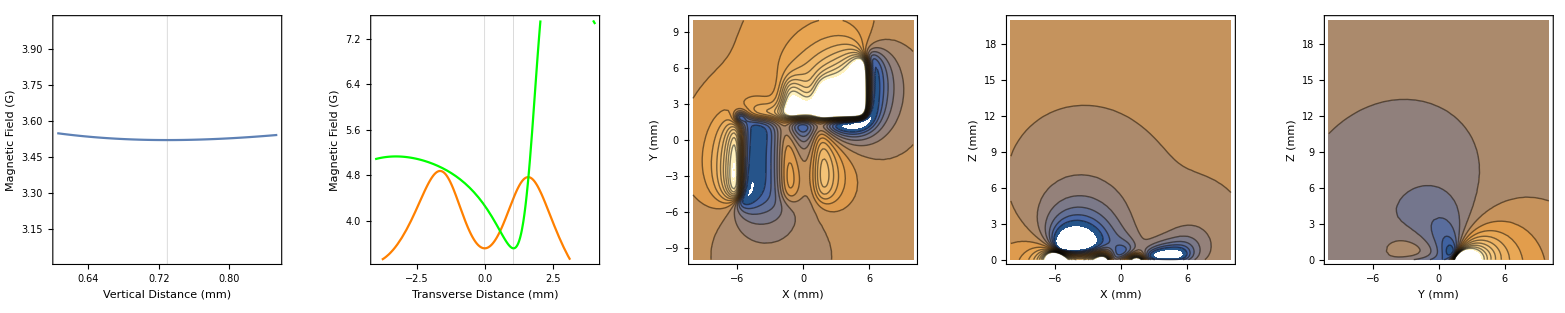

```mathematica
Print[Style["Chip magnetic fields","Subtitle"]];

BoxSize =0.5; (* mm *)

a=GraphicsGrid[{{
Plot1=Plot[BChipMagC2[x1,y1,z mm]/Gauss,{z,1000*#-BoxSize/4,1000*#+BoxSize/4},
Frame->True,Axes->False,
PlotRange->{Bmin1-.5,Bmin1+0.5},
FrameLabel->{"Vertical Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->10,Background->None],
FrameTicksStyle->Directive[FontSize->10,Background->None],
Background->White,GridLines->{{z1/mm},{}},
ImageSize->200
]&[z1],
Plot2=Plot[{
BChipMagC2[x mm,y1,z1]/Gauss,BChipMagC2[x1,x mm,z1]/Gauss},{x,-4.05,4.05},
PlotStyle->{Orange,Green},
Frame->True,Axes->False,
PlotRange->{Bmin1-.2,Bmin1+4.0},
FrameLabel->{"Transverse Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->10,Background->None],
FrameTicksStyle->Directive[FontSize->10,Background->None],GridLines->{{x1/mm,y1/mm},{}},
Background->White,
ImageSize->200
],
ContourPlot[BChipMagC2[x mm,y mm,z1]/Gauss,{x,-10,10},{y,-10,10},Contours->15,FrameLabel->{"X (mm)","Y (mm)"},PlotRange->{Bmin1-.5,Bmin1+4.5}],
ContourPlot[BChipMagC2[x mm,y1,z mm]/Gauss,{x,-10,10},{z,0,20},Contours->15,FrameLabel->{"X (mm)","Z (mm)"},PlotRange->{Bmin1-.5,Bmin1+4.5}],
ContourPlot[BChipMagC2[x1,y mm,z mm]/Gauss,{y,-10,10},{z,0,20},Contours->15,FrameLabel->{"Y (mm)","Z (mm)"},PlotRange->{Bmin1-.5,Bmin1+4.5}]
}}]
```

```mathematica
Beep[];
```

## trap potential

### Deviation from x of background dc field

Overlap between rf B field and vector perpendicular to the static B field

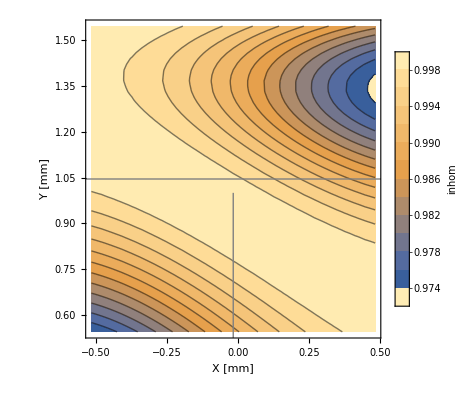
{0.203125,-Graphics-}

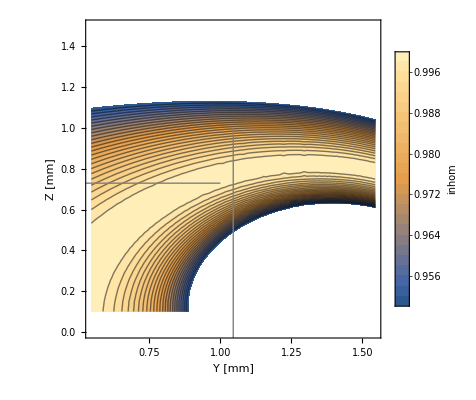

```mathematica
Print@Style["Overlap between rf B field and vector perpendicular to the static B field", "Subtitle"];

ContourPlot[XCosineAccurateC2[x/1000,y/1000,z1],{x,x1/mm-.5,x1/mm+.5},{y,y1/mm-.5,y1/mm+.5},Contours->Table[i,{i,1,.95,-.002}],PlotPoints->15,PlotRange->{.95,1},PlotLegends->BarLegend[All,LegendLabel->"inhom",LabelStyle->{Bold,Gray,16}],
Epilog->{Gray,Thick,Line[{{-1,1000y1},{1,1000y1}}],Gray,Thick,Line[{{1000x1,-1},{1000x1,1.0}}]},
LabelStyle->{Gray,Bold,16},FrameLabel->{"X [mm]","Y [mm]"}]//Timing

ContourPlot[XCosineAccurateC2[x1,y mm,z mm],{y,y1/mm-.5,y1/mm+.5},{z,0.1,1.5},Contours->Table[i,{i,1,.95,-.002}],PlotPoints->15,PlotRange->{.95,1},PlotLegends->BarLegend[All,LegendLabel->"inhom",LabelStyle->{Bold,Gray,16}],
Epilog->{Gray,Thick,Line[{{-1,1000z1},{1,1000z1}}],Gray,Thick,Line[{{1000y1,-1},{1000y1,1.0}}]},
LabelStyle->{Gray,Bold,16},FrameLabel->{"Y [mm]","Z [mm]"}]
```

z component of static B field

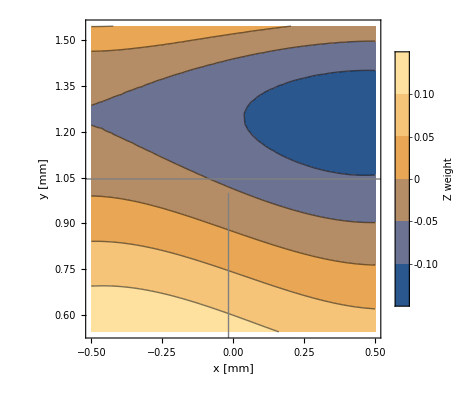

```mathematica
Print@Style["z component of static B field","Subtitle"];

ContourPlot[BChipDirectionC2[x mm,y mm,z1][[3]],{x,-.5,.5},{y,y1/mm-.5,y1/mm+.5},Contours->Table[i,{i,-.2,.2,.05}],PlotLegends->BarLegend[All,LegendLabel->"Z weight",LabelStyle->Directive[Brown,FontSize->14,Italic]],Epilog->{Gray,Thick,Line[{{-1,1000y1},{1,1000y1}}],Gray,Thick,Line[{{1000x1,-1},{1000x1,1.0}}]},LabelStyle->{Gray,Bold,16},FrameLabel->{"x [mm]","y [mm]"}]
```

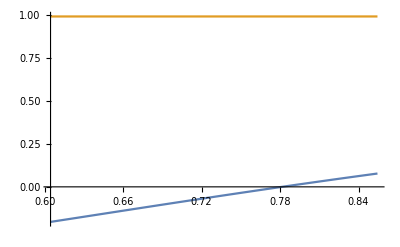

```mathematica
Plot[{BChipDirectionC2[x1, y1, z mm][[3]],mwUnitVec[x1,y1,z mm][[3]]}, {z,z1*1000-BoxSize/4,z1*1000+BoxSize/4}]
```

```mathematica
Plot[{BChipDirectionC2[x1,y1,z mm]⟦3⟧,mwUnitVec[x1,y1,z mm]⟦3⟧},{z,z1 1000-BoxSize/4,z1 1000+BoxSize/4}]
```

-Graphics-

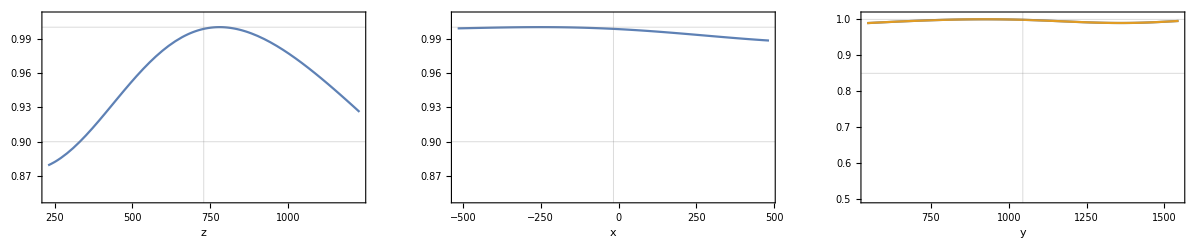

```mathematica
GraphicsGrid[{{
Plot[XCosineAccurateC2[x1,y1,z μm],{z,z1/μm-1000/2,z1/μm+1000/2},AxesOrigin->{z1/μm,0},Axes->False,Frame->True,GridLines->{{z1/μm},{.9,1.0}},PlotRange->{.85,1.01},FrameLabel->{"z"}],
Plot[XCosineAccurateC2[x μm,y1,z1],{x,x1/μm-1000/2,x1/μm+1000/2},Axes->False,Frame->True,GridLines->{{x1/μm},{.9,1.0}},PlotRange->{0.85,1.01},FrameLabel->{"x"}],
Plot[{XCosineAccurateC2[x1,y μm,z1],
XCosineAccurateC2[x1,y μm,z1]},{y,y1/μm-1000/2,y1/μm+1000/2},Axes->False,Frame->True,GridLines->{{y1/μm},{.85,1.0}},PlotRange->{0.5,1.01},FrameLabel->{"y"}]}}]
```

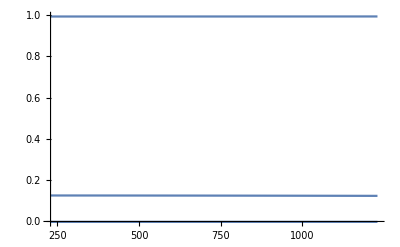

```mathematica
Plot[mwUnitVec[x1,y1,z μm],{z,#-500,#+500}]&[z1/μm]
```

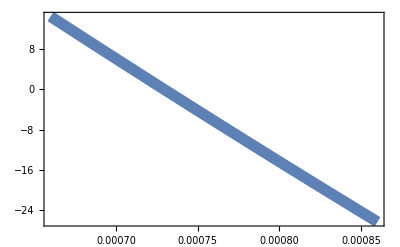

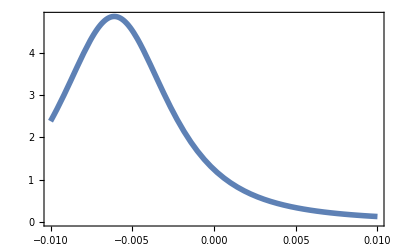

```mathematica
(* Check the form of the rf field around the trap center. *)
 Plot[(h /kb/1*^-9)(15000Bmagmw[z,mwLoopOriginZ,1*^-10,.005]/Bmagmw[z1,mwLoopOriginZ,1*^-10,.005] - 15000),{z,0.000660,.000860},Frame->True,Axes->False,PlotStyle->Thickness[.02]]
Plot[(Bmagmw[z,mwLoopOriginZ,x1+.00001,.005]/Bmagmw[z1,mwLoopOriginZ,x1+.00001,.005] ),{z,-.010,.010},Frame->True,Axes->False,PlotStyle->Thickness[.01](*,GridLines->{{0,z1},{1.0,z1}}*)]
```

### Definition of adiabatic potentials; rotating-frame + RWA (this is equivalent to Δ’ Fz + (Ω/2) Fx + Zeeman energies (note Perrin/Garraway papers just use Ω_0 Fx)

I think that it should be -Δ’ Fz + (Ω/2) Fx   + Zeeman energies.

Δ’, which is generally spatially-dependent, is the detuning between the microwave frequency and the local energy splitting, Δ'=ω_μW-(1/ℏ)(E_22(r)-E_11(r)) (N.B. here it is defined as a radial frequency, while in the code it is always in Hertz). In the code this is appears as the sum between a global detuning defined with reference to that transition in the absence of an external magnetic field (~7 GHz) and the shifts caused by its presence (~6 MHz).

In the Perrin & Garraway works, Δ’ is identified as the Larmor frequency, and I’m still double-checking what that should be in the microwave case.

A quick derivation of the form used below:

Δ'=ω_mW-ω_atm(r)=ω_mW-(ω_0-δ_Zeeman(r))=Δ+δ_Zeeman(r)

And note that the terms on the diagonal are of the form mΔ’, where m is the index of the hyperfine sublevel.

The relevant experimental value is usually the detuning defined relative to the transition frequency at the center of the trap where the field magnitude is B0. So when Δ is set equal to zeemanShiftOnly[B0], the diagonal elements of the Hamiltonian become the detuning relative to the center of the trap.

Moral of the story: Δ is a strange way to parameterize the Hamiltonian and a holdout from the rf version of the model. When Δ is set equal to zeemanShiftOnly[B0], the microwave field is resonant with the center of the trap. Anything added to zeemanShiftOnly[B0] is thus the detuning relative to that value.

```mathematica
Clear[rwaHamiltonian,rwaHamiltonianC,AdiabaticEnergiesChipC,AdiabaticEnergiesChipC2,AdiabaticEnergiesChipC2All]
(* Δ = Subscript[ν, μW] - Subscript[ν, 0], where Subscript[ν, 0] is the frequency of the |1,1>->|2,2> transition in the absence of an external magnetic field. *)
(* for the following it will be useful to introduce the function zeemanShiftOnly, which gives the frequency [Hz] by which the transition frequency (|1,1>->|2,2>) is shifted from its zero field value by a magnetic field of magnitude field [T]. *)
(* Note that the first element of the Hamiltonian corresponds to the <1,1|H|1,1> element. *)
zeemanShiftOnly[field_]:=(ZeemanShiftF2[field][[5]]-ZeemanShiftF2[0][[5]])-(ZeemanShiftF1[field][[3]]-ZeemanShiftF1[0][[3]]);
zeemanShiftOnlyC[field_]:=(ZeemanShiftF2C[field][[5]]-ZeemanShiftF2C[0][[5]])-(ZeemanShiftF1C[field][[3]]-ZeemanShiftF1C[0][[3]]);

ClearAll[ℏ,μB,Bc,gJs,gIs,Δ,Ω,ahf];
(* Clear that constants that will be used to define the symbolic Hamiltonian, using Greek characters where applicable and append "s" ("symbol") on Roman characters. *)
rwaHamiltonianSymb=((ahf/ℏ^2)*idjf+(μB*Bc/ℏ)*(gJs*jzf+gIs*izf)-(2*Pi*Δ+2*ahf/ℏ)*fzf+(Ω/Sqrt[2])*(-(gJs*jp1f+gIs*ip1f)+(gJs*jm1f+gIs*im1f)));

hamiltonianValSubs={ℏ->hbar,μB->muB,Bc->BChipMag[x,y,z],gJs->gJS12,gIs->gI,ahf->ahfsS12};
hamiltonianValSubsC2={ℏ->hbar,μB->muB,Bc->BChipMagC2[x,y,z],gJs->gJS12,gIs->gI,ahf->ahfsS12}; (* The only change to this from the previous variable is BChipMag -> BChipMagC2. *)
```

```mathematica
FullSimplify@rwaHamiltonianSymb//MatrixForm
```

(-(13 ahf)/4+1/2 Bc (3 gIs+gJs) μB-4 π Δ ℏ | 1/4 (3 gIs+gJs) Ω ℏ | 0 | 0 | 0 | 1/4 √3 (-gIs+gJs) Ω ℏ | 0 | 0
1/4 (3 gIs+gJs) Ω ℏ | 1/4 (-5 ahf+Bc (3 gIs+gJs) μB-8 π Δ ℏ) | 1/4 √(3/2) (3 gIs+gJs) Ω ℏ | 0 | 0 | 1/4 √3 Bc (gIs-gJs) μB | 1/4 √(3/2) (-gIs+gJs) Ω ℏ | 0
0 | 1/4 √(3/2) (3 gIs+gJs) Ω ℏ | (3 ahf)/4 | -1/4 √(3/2) (3 gIs+gJs) Ω ℏ | 0 | ((gIs-gJs) Ω ℏ)/(4 √2) | 1/2 Bc (gIs-gJs) μB | ((gIs-gJs) Ω ℏ)/(4 √2)
0 | 0 | -1/4 √(3/2) (3 gIs+gJs) Ω ℏ | 1/4 (11 ahf-Bc (3 gIs+gJs) μB+8 π Δ ℏ) | 1/4 (3 gIs+gJs) Ω ℏ | 0 | 1/4 √(3/2) (-gIs+gJs) Ω ℏ | 1/4 √3 Bc (gIs-gJs) μB
0 | 0 | 0 | 1/4 (3 gIs+gJs) Ω ℏ | (19 ahf)/4-1/2 Bc (3 gIs+gJs) μB+4 π Δ ℏ | 0 | 0 | 1/4 √3 (gIs-gJs) Ω ℏ
1/4 √3 (-gIs+gJs) Ω ℏ | 1/4 √3 Bc (gIs-gJs) μB | ((gIs-gJs) Ω ℏ)/(4 √2) | 0 | 0 | 1/4 (-13 ahf+Bc (5 gIs-gJs) μB-8 π Δ ℏ) | ((5 gIs-gJs) Ω ℏ)/(4 √2) | 0
0 | 1/4 √(3/2) (-gIs+gJs) Ω ℏ | 1/2 Bc (gIs-gJs) μB | 1/4 √(3/2) (-gIs+gJs) Ω ℏ | 0 | ((5 gIs-gJs) Ω ℏ)/(4 √2) | -(5 ahf)/4 | ((-5 gIs+gJs) Ω ℏ)/(4 √2)
0 | 0 | ((gIs-gJs) Ω ℏ)/(4 √2) | 1/4 √3 Bc (gIs-gJs) μB | 1/4 √3 (gIs-gJs) Ω ℏ | 0 | ((-5 gIs+gJs) Ω ℏ)/(4 √2) | 1/4 (3 ahf+Bc (-5 gIs+gJs) μB+8 π Δ ℏ))

```mathematica
(* Take care making the variable substitution to get numerical expressions: the Evaluate function is necessary, and the (1/h) term must be inside of it. *)
rwaHamiltonian[Δ_,Ω_,x_,y_,z_]:=(Evaluate[(1/h)*rwaHamiltonianSymb/.hamiltonianValSubs]);

rwaHamiltonianC[Δ_,Ω_,x_,y_,z_]:=(Evaluate[(1/h)*rwaHamiltonianSymb/.hamiltonianValSubsC2]); (* Another numerical expression of the rotating wave Hamiltonian, this time defined in terms of the compiled BChipMag function, BChipMagC2. *)

AdiabaticEnergiesChipSlow[Δ_,Ω_,x_,y_,z_]:=Eigensystem[rwaHamiltonian[Δ,Ω,x,y,z]][[1,3]];

AdiabaticEnergiesChipC[Δ_,Ω_,x_,y_,z_]:=Eigensystem[rwaHamiltonianC[Δ,Ω,x,y,z]][[1,3]];

AdiabaticEnergiesChipC2[Δ_?NumericQ,Ω_?NumericQ,x_?NumericQ,y_?NumericQ,z_?NumericQ]:=AdiabaticEnergiesChipC[Δ, Ω,x,y,z ];

AdiabaticEnergiesChipCAll[Δ_,Ω_,x_,y_,z_]:=Eigenvalues@rwaHamiltonianC[Δ,Ω,x,y,z];  

AdiabaticEnergiesChipC2All[Δ_?NumericQ,Ω_?NumericQ,x_?NumericQ,y_?NumericQ,z_?NumericQ]:=AdiabaticEnergiesChipCAll[Δ, Ω,x,y,z ];

AdiabaticVectorsChipC[Δ_,Ω_,x_,y_,z_]:=Eigenvectors@rwaHamiltonianC[Δ,Ω,x,y,z];  

AdiabaticEnergiesChipAll[Δ_,Ω_,x_,y_,z_]:=Eigenvalues@rwaHamiltonian[Δ,Ω,x,y,z];

esystem[Δ_,Ω_,x_,y_,z_]:=Eigensystem@rwaHamiltonian[Δ,Ω,x,y,z];

Beep[];
Pause[1];
Beep[];
```

## calculate some potentials!

Whereas before Δguess was the resonant frequency of the rf transition at the center of the trap, it is now just the Zeeman shift caused by the magnetic field at that point.

The resonance microwave frequency is given by the following

```mathematica
Print["Resonance at trap center [GHz] : "<>ToString[(ZeemanShiftF2C[#][[5]]-ZeemanShiftF1C[#][[3]])/(10^9)&[B0]]];
```

Resonance at trap center [GHz] : 6.84208

```mathematica
Δguess=zeemanShiftOnlyC[B0]
```

7.40104×10^6

```mathematica
BChipMagC2[x1,y1,z1-160*10^(-6)]/Gauss
BChipMagC2[x1,y1,z1+235*10^(-6)]/Gauss
```

3.56915

3.58599

```mathematica
(* Calc. the mag. field gradient at a given point in z *)
deltaZTemp=(*235*10^(-6);*)-160*10^(-6);
deltaTemp = 1*10^(-9);
(BChipMagC2[x1,y1,z1+deltaZTemp+deltaTemp]-BChipMagC2[x1,y1,z1+deltaZTemp-deltaTemp])/(2*deltaTemp*Gauss)
```

-656.299

```mathematica
11.1163*10^9/(2*ahfsS12/h)
```

1.62645

```mathematica
6.84208*10^9-2*ahfsS12/h
```

7.39679×10^6

```mathematica
zeemanShiftOnlyC[BChipMag[x1,y1,z1]]
```

7.40104×10^6

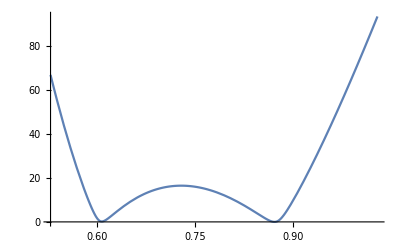

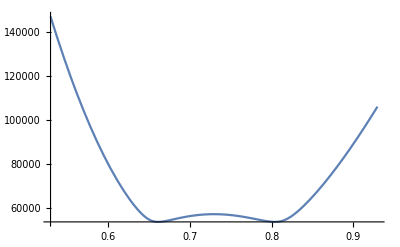

```mathematica
Δ1=(*6.84208*10^9-2*ahfsS12/h*)zeemanShiftOnlyC[BChipMag[x1,y1,z1]]+60*^3;

Ωc =     1.0 16.983*^3;   (* rabi frequency [Hz] *) 
Ωc =   (2*Pi)*5*^3; (* Rabi frequency [Hz] *)
Clear[testf];
testf[x_,y_,z_]:=AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z] mwMagFracC2[x,y,z ]   ,x,y,z];
t= Table[{z,testf[x1,y1,z]},{z,z1-1.2 mm,z1+1.2mm,0.125*^-6}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
(* CHECK WHERE ZMIN IS USED IN PREVIOUS VERSIONS *)
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
ShiftVal=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,y1,zmin]mwMagFracC2[x1,y1,zmin ],x1,y1,zmin];
testf[x1,y1,z1]nKPerHz;
Ububble[x_,y_,z_]:= testf[x,y,z]-ShiftVal;
Ububble5[x_,y_,z_]:= Evaluate[testf[x,y,z]-ShiftVal];
(*Ububble50[x_,y_,z_]:=Evaluate[testf[x,y,z]-ShiftVal];*)
(*Ububble500[x_,y_,z_]:= Evaluate[testf[x,y,z]-ShiftVal];*)
Plot[Ububble[x1,y1,z/1000]/10^3,{z,(z1-.0002)*1000,(z1+.0003)*1000}(*,PlotRange->{0,10000}*)]
Plot[AdiabaticEnergiesChipC2[Δ1-40000,Ωc,x1,y1,z/1000]-ShiftVal,{z,(z1-.0002)*1000,(z1+.0002)*1000}(*,PlotRange->{0,10000}*)]
```

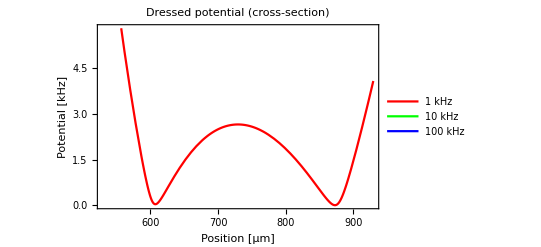

```mathematica
Show@MapThread[
Plot[#1[x1,y1,z/(10^6)]/(2*Pi*10^3),{z,(z1-.0002)*10^6,(z1+.0002)*10^6},
(*PlotRange->{0,10000/(2*Pi*10^3)},*)
PlotStyle->{#2,Thick},
PlotLegends->LineLegend[{#3},LegendLabel->If[#3=="1 kHz","rf Rabi freq",None]],
PlotLabel->"Dressed potential (cross-section)",
FrameLabel->{"Position [μm]","Potential [kHz]"},
Frame->True
]&,
{{Ububble5,Ububble50,Ububble500},{Red,Green,Blue},{"1 kHz","10 kHz", "100 kHz"}}
]
```

```mathematica
testf[x1,y1,z1]
```

-1.11163×10^10

```mathematica
Δ1
```

7.46104×10^6

delta [MHz] = 7.45679

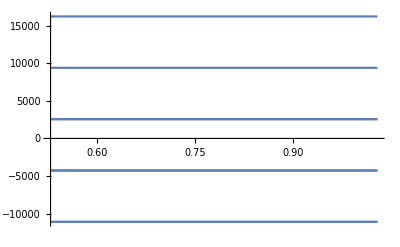

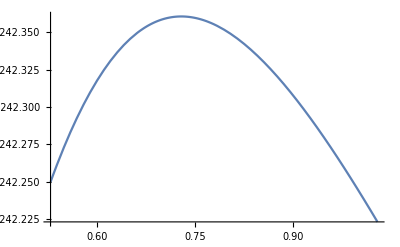
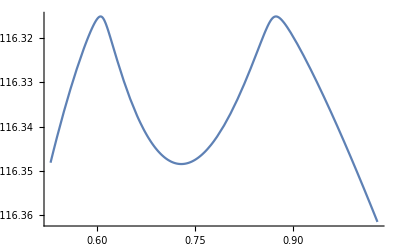
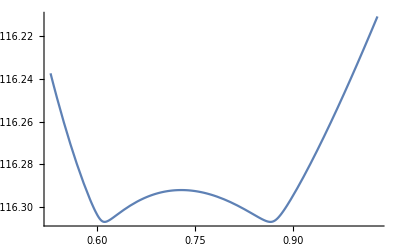
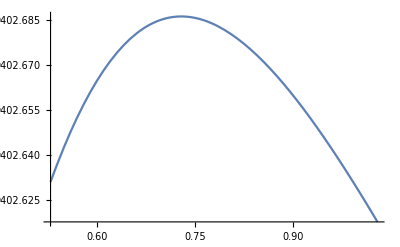
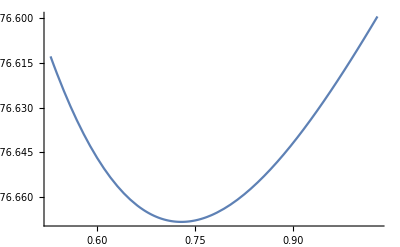
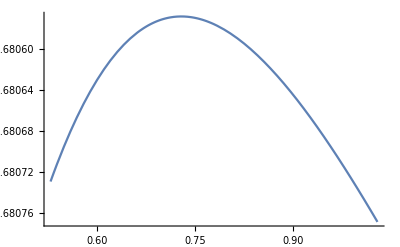
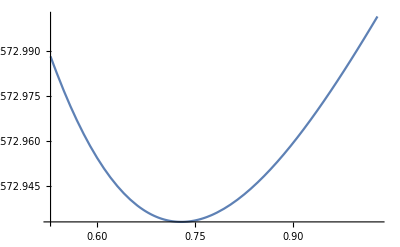

-Graphics-

```mathematica
deltaTemp=6.84208*10^9-2*ahfsS12/h+60*^3;
Print["delta [MHz] = "<>ToString[deltaTemp/10^6]];
Plot[AdiabaticEnergiesChipC2All[deltaTemp,Ωc,x1,y1,z/1000]/10^6,{z,(z1-.0002)*1000,(z1+.0003)*1000}]
Plot[AdiabaticEnergiesChipAll[deltaTemp,Ωc,x1,y1,z/1000][[#]]/10^6,{z,(z1-.0002)*1000,(z1+.0003)*1000}]&/@Range[8]
Plot[AdiabaticEnergiesChipAll[deltaTemp,Ωc,x1,y1,z/1000][[{2,3}]]/10^6,{z,(z1-.0002)*1000,(z1+.0003)*1000}]
Plot[AdiabaticEnergiesChipAll[deltaTemp,Ωc,x1,y1,z/1000]/10^6,{z,(z1-.0002)*1000,(z1+.0003)*1000}]
```

```mathematica
Chop@Threshold[#*Conjugate[#],0.0001]&/@(esystem[deltaTemp,Ωc,x1,y1,z1][[2,{2,3}]])
```

{{0.994051,0,0,0,0,0.00594946,0,0},{0.00594946,0,0,0,0,0.99405,0,0}}

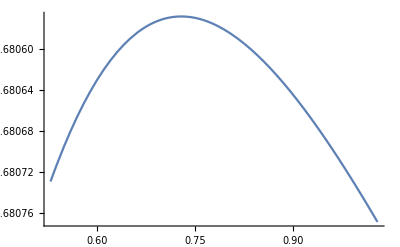
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[esystem[deltaTemp,Ωc,x1,y1,z/1000][[1,#]]/10^6,{z,(z1-.0002)*1000,(z1+.0003)*1000}]&/@Range[8]
```

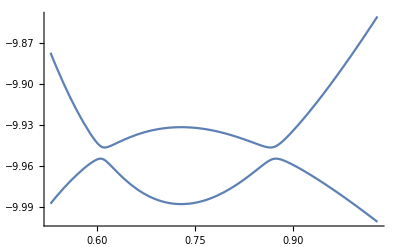

```mathematica
Plot[(AdiabaticEnergiesChipAll[deltaTemp,Ωc,x1,y1,z/1000][[{2,3}]]+(1+5/8)*2*ahfsS12/h)/10^6,{z,(z1-.0002)*1000,(z1+.0003)*1000}]
```

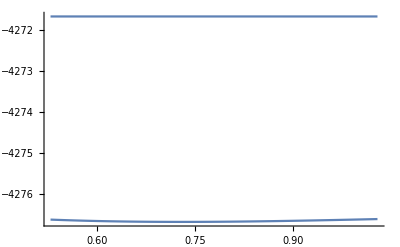

```mathematica
Plot[AdiabaticEnergiesChipAll[deltaTemp,Ωc,x1,y1,z/1000][[{5,6}]]/10^6,{z,(z1-.0002)*1000,(z1+.0003)*1000}]
```

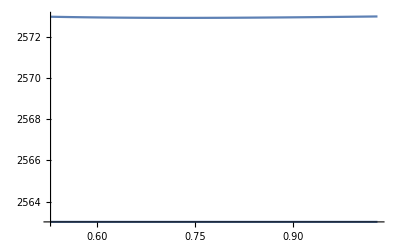

```mathematica
Plot[AdiabaticEnergiesChipAll[deltaTemp,Ωc,x1,y1,z/1000][[{7,8}]]/10^6,{z,(z1-.0002)*1000,(z1+.0003)*1000}]
```

```mathematica
dressedPotential[x_, y_, z_]:=AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x,y,z] mwMagFracC2[x,y,z],x,y,z];
fitRange = 1;(* [mm] *)

fxminp = (FindMinimum[{(-ShiftVal+ dressedPotential[x mm, y1, z1]),#*1000≤x≤#*1000+fitRange},{x,#*1000}]&[x1])[[1]];
fxminn = (FindMinimum[{(-ShiftVal+ dressedPotential[x mm, y1, z1]),#*1000-fitRange≤x≤#*1000},{x,#*1000}]&[x1])[[1]];
fxmin = Min[{fxminp, fxminn}];

fyminp = (FindMinimum[{(-ShiftVal+ dressedPotential[x1, y mm, z1]),#*1000≤y≤#*1000+fitRange},{y,#*1000}]&[y1])[[1]];
fyminn = (FindMinimum[{(-ShiftVal+ dressedPotential[x1, y mm, z1]),#*1000-fitRange≤y≤#*1000},{y,#*1000}]&[y1])[[1]];
fymin = Min[{fyminp, fyminn}];

fzminp = (FindMinimum[{(-ShiftVal+ dressedPotential[x1, y1, z mm]),#*1000≤z≤#*1000+fitRange},{z,#*1000}])&[z1][[1]];
fzminn = (FindMinimum[{(-ShiftVal+ dressedPotential[x1, y1, z mm]),#*1000-fitRange≤z≤#*1000},{z,#*1000}])&[z1][[1]];
fzmin = Min[{fzminp,fzminn}];

Print["At rf Delta = "<>ToString[(Δ1-Δguess)*10^(-3)]<>" kHz:"];
Print["x minima difference: "<>ToString[Abs[fxminp-fxminn]]<>" Hz"];
Print["y minima difference: "<>ToString[Abs[fyminp-fyminn]]<>" Hz"];
Print["z minima difference: "<>ToString[Abs[fzminp-fzminn]]<>" Hz"];
Print["max minima difference: "<>ToString[Max@#-Min@#]<>" Hz"]&[{fxminp,fxminn,fyminp,fyminn,fzminp,fzminn}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

At rf Delta = 60. kHz:

x minima difference: 17.0879 Hz

y minima difference: 33.6462 Hz

z minima difference: 198.502 Hz

max minima difference: 198.502 Hz

```mathematica
BoxSize =0.5; (* mm *) (* Also defined above to look at the magnetic field ! *)
```

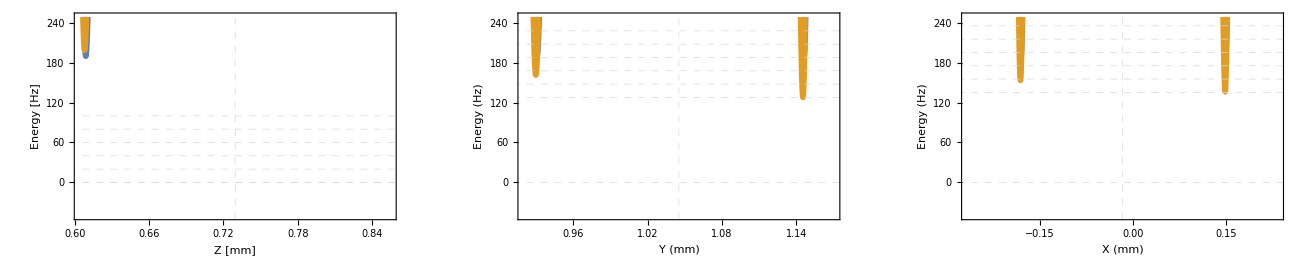

```mathematica
defaultPlotOptions=Options[Plot];

SetOptions[Plot, 
PlotStyle->Thickness[.01],PlotPoints->300,FrameStyle->Directive[Black,12,FontFamily->"Century Gothic"],Axes->False,Frame->True,
PlotRange->{#1-50,#2+50}&[Min[{fxmin,fymin,fzmin}],Max@{fxminp,fxminn,fyminp,fyminn,fzminp,fzminn}]];

GraphicsGrid[{{
Plot[{
(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  ,x1,y1,z/1000-1*^-6]),
(-ShiftVal+ dressedPotential[x1, y1, z mm])
},
{z,1000z1-BoxSize/4,1000z1+BoxSize/4},
GridLines->{{1000z1},{0}~Join~(Range[0,100,20]+fzmin)},
GridLinesStyle->Dashed,
FrameLabel->{"Z [mm]","Energy [Hz]"}(*,
PlotRange->All*)],

Plot[{
(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  ,x1,y mm-1*^-6,z1]),
(-ShiftVal+dressedPotential[x1, y mm, z1])
},
{y,y1/mm-BoxSize/4,y1/mm+BoxSize/4},
GridLines->{{1000y1},{0}~Join~(Range[0,100,20]+fymin)},
GridLinesStyle->Dashed,
FrameLabel->{"Y (mm)","Energy (Hz)"}],

Plot[{
(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  ,x/1000-1*^-6,y1,z1]),
(-ShiftVal+1+dressedPotential[x mm, y1, z1])
},
{x,x1/mm-BoxSize/2, x1/mm+BoxSize/2},
GridLines->{{1000x1},{0}~Join~(Range[0,100,20]+fxmin)},
GridLinesStyle->Dashed,
FrameLabel->{"X (mm)","Energy (Hz)"}]}},ImageSize->1300]

SetOptions[Plot,defaultPlotOptions];
```

```mathematica
bubble3D[x_, y_, z_]:=Evaluate[-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x mm,y mm,z mm]mwMagFracC2[x mm,y mm,z mm] ,x mm,y mm,z mm]];
```

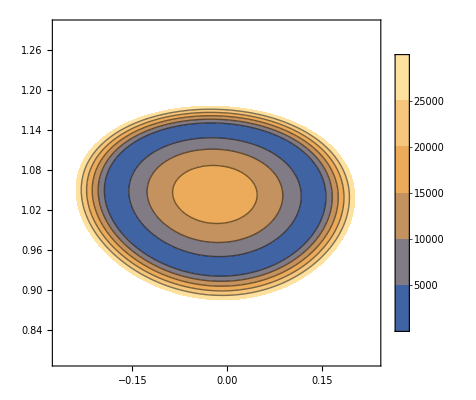

```mathematica
zShift=0.01; (* mm *)
ContourPlot[bubble3D[x,y,z1/mm-zShift],{x,x1/mm-BoxSize/2,x1/mm+BoxSize/2},{y,y1/mm-BoxSize/2,y1/mm+BoxSize/2},PlotLegends->Automatic,PlotRange->{-50,30000}]
```

```mathematica
ftight =150;
fweak = 50;
AtomNumber =200000;
fbar = (ftight  ftight fweak)^.33333;
abar= Sqrt[hbar/(mRb 2 π fbar)];
μ= (hbar 2 π fbar/2)(15 AtomNumber (100.4 .529177*^-10)/abar)^(2/5);
Print[μnK = μ /kb/1*^-9 //Round , " nK"] 
Print[μHz =μnK 21 //Round, " Hz"] 
Print["Tight TF radius = ", Round[1*^6 Sqrt[2μ/(mRb 4 π^2 ftight^2)]], " μm"]
Print["Loose TF radius = ", Round[1*^6 Sqrt[2μ/(mRb 4 π^2 fweak^2)]], " μm"]
```

117 nK

2457 Hz

Tight TF radius = 5 μm

Loose TF radius = 15 μm

```mathematica
graining = .1*^-6;
t= Table[{z,testf[x1,y1,z]},{z,z1-.5 mm,z1+.001mm,graining}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
minval = t[[minloc,2]] h/kb/1*^-9;
Print[minval, " nK at location z = ",1000 zmin, " mm"]
Print["fz = ",fz = Sqrt[h(t[[minloc+1,2]]-2t[[minloc,2]]+t[[minloc-1,2]])/graining^2/mRb]/2/π, " Hz"]
Print["SHO minimum ", SHOnKz=h fz/kb/1*^-9/2, " nK, ", fz/2, " Hz"]
minval+SHOnKz //Round
```

-5.33499×10^8 nK at location z = 0.608481 mm

fz = 164.144 Hz

SHO minimum 3.93885 nK, 82.0722 Hz

-533498756

```mathematica
graining = .1*^-6;
t= Table[{z,testf[x1,y1,z]},{z,z1-.001 mm,z1+3.0mm,graining}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
minval = t[[minloc,2]] h/kb/1*^-9;
Print[minval, " nK at location z = ",1000 zmin, " mm"]
Print["fz = ",fz = Sqrt[h(t[[minloc+1,2]]-2t[[minloc,2]]+t[[minloc-1,2]])/graining^2/mRb]/2/π, " Hz"]
Print["SHO minimum ", SHOnKz=h fz/kb/1*^-9/2, " nK, ", fz/2, " Hz"]
minval+SHOnKz //Round
```

147.446 nK at location z = 0.785981 mm

fz = 66.5498 Hz

SHO minimum 1.59694 nK, 33.2749 Hz

149

```mathematica
ty= Table[{y,testf[x1,y,z1]},{y,y1-.001,y1+0.001,graining}];
minlocy= Position[ty[[All,2]],Min[ty[[All,2]]]][[1,1]];
ymin = ty[[Position[ty[[All,2]],Min[ty[[All,2]]]][[1,1]],1]];
minvaly = ty[[minlocy,2]] h /kb/1*^-9;
Print[minvaly, " nK at location y = ",1000 ymin, " mm"]
Print["fy = ",fy=Sqrt[h(ty[[minlocy+1,2]]-2ty[[minlocy,2]]+ty[[minlocy-1,2]])/graining^2/mRb]/2/π]
Print["SHO minimum ", SHOnKy=h fy/kb/1*^-9/2, " nK, ", fy/2, " Hz"]
minvaly+SHOnKy //Round
```

148.944 nK at location y = 1.08879 mm

fy = 91.3246

SHO minimum 2.19144 nK, 45.6623 Hz

151

```mathematica
tx= Table[{x,testf[x,y1,z1]},{x,x1-.001,x1+0.001,graining}];
minlocx= Position[tx[[All,2]],Min[tx[[All,2]]]][[1,1]];
xmin = tx[[Position[tx[[All,2]],Min[tx[[All,2]]]][[1,1]],1]];
minvalx = tx[[minlocx,2]]h /kb/1*^-9;
Print[minvalx, " nK at location yx= ",1000 xmin, " mm"]
Print["fx = ",fx=Sqrt[h(tx[[minlocx+1,2]]-2tx[[minlocx,2]]+tx[[minlocx-1,2]])/graining^2/mRb]/2/π]
Print["SHO minimum ", SHOnKx=h fx/kb/1*^-9/2, " nK, ", fx/2, " Hz"]
minvalx+ SHOnKx //Round
```

149.075 nK at location yx= 0.0525256 mm

fx = 55.8027

SHO minimum 1.33905 nK, 27.9013 Hz

150

```mathematica
λ = 10064*^-9;
```

```mathematica
a1= ContourPlot[0 3000 Sin[2 π x mm/λ]^2 1*^9(h/kb)+(-ShiftVal+AdiabaticEnergiesChipC2[Δ1,Ωc XCosineAccurateC2[x/1000,y/1000,z1] mwMagFracC2[x/1000,y/1000,z1]  ,x/1000,y/1000,z1]),
{x,1000x1-BoxSize/2,1000x1+BoxSize/2},{y,1000y1-BoxSize/4,1000y1+BoxSize/4},
PlotRange->{-500,1000},
AspectRatio->1/2,
Contours->Table[i,{i,-500,1000,100}],
PlotPoints->102,ImageSize->1000,
FrameLabel->{"X (mm)","Y (mm)"},
FrameStyle->Directive[Thick,Black,12,FontFamily->"Century Gothic"],
Axes->False,
Epilog->{Red,Thin,Line[{{1000x1-.2,1000y1},{1000x1+.2,1000y1}}],Red,Thin,Line[{{1000x1,1000y1-.21},{1000x1,1000y1+.2}}]}]  (*takes ~10s to generate *)
```

-Graphics-

```mathematica
ContourPlot[nKPerHz(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x/1000,y1,z/1000] mwMagFracC2[x/1000,y1,z/1000],x/1000,y1,z/1000]),{x,1000x1-BoxSize/2,1000x1+BoxSize/2},
{z,1000z1-BoxSize/4,1000z1+BoxSize/4},
PlotRange->{-100,200},ImageSize->1000,
Contours->Table[i,{i,-100,200,10}],PlotPoints->140,
FrameLabel->{"X (mm)","Z (mm)"},
FrameStyle->Directive[Thick,Black,12,FontFamily->"Century Gothic"],
Axes->False,AspectRatio->1/2,
Epilog->{Red,Thickness[.0005],Line[{{-.2,1000z1},{.2,1000z1}}],Red,Thickness[.0005],Line[{{1000x1,.2},{1000x1,1.0}}]}]  (*takes ~10s to generate *)   (* GridLines->{Table[i,{i,x1/mm-.08,x1/mm+.08,.0045}],Table[i,{i,z1/mm-.04,z1/mm+.04,.0045}]} *)
```

-Graphics-

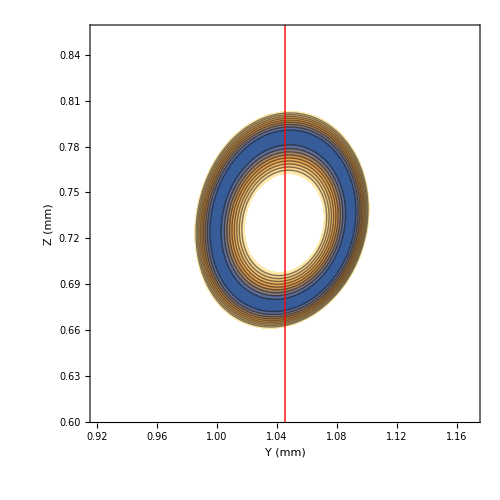

```mathematica
a1= ContourPlot[nKPerHz(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x1,y/1000,z/1000] mwMagFracC2[x1,y/1000,z/1000],x1,y/1000,z/1000]),{y,1000y1-BoxSize/4,1000y1+BoxSize/4},
{z,1000z1-BoxSize/4,1000z1+BoxSize/4},PlotRange->{-100,200},
Contours->Table[i,{i,-100,200,20}],PlotPoints->40,
AspectRatio->1,
ImageSize->500,
FrameLabel->{"Y (mm)","Z (mm)"},
FrameStyle->Directive[Thick,Black,12,FontFamily->"Century Gothic"],
Axes->False,Epilog->{Red,Thin,Line[{{-.2,1000z1},{.1,1000z1}}],Red,Thin,Line[{{1000y1,.4},{1000y1,1.0}}]}]  (*takes ~10s to generate *)
```

```mathematica
Print["z1 = ", Round[1*^6 z1], " microns"]
```

z1 = 729 microns

```mathematica
Δ1= 1.969*^6;
Δ1 =1.97*^6; 
Δ1 = 3.8935*^6;
Δ1 = 3.897*^6;
Δ1 =3.909036*^6;
Δ1= 1.786*^6;
Δ1=2.647*^6;
Δ1=1.350*^6;
Δ1= 1.375*^6;
Δ1=2.540*^6+40*^3;
Δ1=2.500*^6+0*^3;

Δ1=3.728*^6;

Δ1=1.970*^6;
Δ1=1.970*^6+40*^3;

Δ1=Δguess+30*^3;



Ωc = .25   16.983*^3;   (* rabi frequency *)  (* taken from German's current of like .02A or something, but with loop coplanar with chip *)
Ωc =5*^3;(* rabi frequency *)
```

## Test

```mathematica
TestBECPotential[x_,y_,z_,ω_]:= (1/2) (mRb/h) ω^2 (x^2+y^2+z^2)
```

```mathematica
fTest= 100;
```

```mathematica
potential0 = Table[TestBECPotential[x,y,z,2Pi fTest],
{z,-CubeSize/4,+CubeSize/4,DataFileGraining},
{y,-CubeSize/4,+CubeSize/4,DataFileGraining},
{x,-CubeSize/2,+CubeSize/2,DataFileGraining}];
```

Table::iterb: Iterator {z,-CubeSize/4,CubeSize/4,DataFileGraining} does not have appropriate bounds.

```mathematica
Dimensions[potential0]
```

{4}

```mathematica
potential0[0,0,z1-CubeSize/4,628]
```

Table[TestBECPotential[x,y,z,2 π fTest],{z,-CubeSize/4,CubeSize/4,DataFileGraining},{y,-CubeSize/4,(+CubeSize)/4,DataFileGraining},{x,-CubeSize/2,(+CubeSize)/2,DataFileGraining}][0,0,0.000729481-CubeSize/4,628]

```mathematica
ListPlot[potential0[[51,;;,101]]]
```

Part::partw: Part 51 of Table[TestBECPotential[x,y,z,2 π fTest],{z,-CubeSize/4,CubeSize/4,DataFileGraining},{y,-CubeSize/4,(+CubeSize)/4,DataFileGraining},{x,-CubeSize/2,(+CubeSize)/2,DataFileGraining}] does not exist.

Table::iterb: Iterator {z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining} does not have appropriate bounds.

Part::partw: Part 51 of Table[TestBECPotential[x,y,z,2. 3.141592653589793 fTest],{z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining},{y,(-1. CubeSize) 0.25,+CubeSize 0.25,DataFileGraining},{x,(-1. CubeSize) 0.5,+CubeSize 0.5,DataFileGraining}] does not exist.

Table::iterb: Iterator {z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining} does not have appropriate bounds.

Part::partw: Part 51 of Table[TestBECPotential[x,y,z,2. 3.14159 fTest],{z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining},{y,(-1. CubeSize) 0.25,+CubeSize 0.25,DataFileGraining},{x,(-1. CubeSize) 0.5,+CubeSize 0.5,DataFileGraining}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: Table[TestBECPotential[x,y,z,2. 3.14159 fTest],{z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining},{y,(-1. CubeSize) 0.25,+CubeSize 0.25,DataFileGraining},{x,(-1. CubeSize) 0.5,+CubeSize 0.5,DataFileGraining}]⟦51,1;;All,101⟧ is not a list of numbers or pairs of numbers.

ListPlot[Table[TestBECPotential[x,y,z,2 π fTest],{z,-CubeSize/4,CubeSize/4,DataFileGraining},{y,-CubeSize/4,(+CubeSize)/4,DataFileGraining},{x,-CubeSize/2,(+CubeSize)/2,DataFileGraining}]⟦51,1;;All,101⟧]

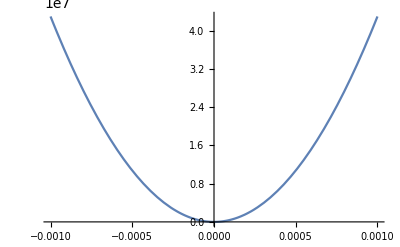

```mathematica
Plot[TestBECPotential[0,0,x,2 Pi 100],{x,-.001,.001}]
```

```mathematica
potential0a=Flatten[potential0,1];
Dimensions[potential0a]
FileString0=StringJoin["TestPotential_",ToString[1000DataFileGraining/μm//Round],"u_",ToString[fTest //Round],"Hz",".csv"]
"TestPotential_250u_100Hz.csv"
```

Table::iterb: Iterator {z,-CubeSize/4,CubeSize/4,DataFileGraining} does not have appropriate bounds.

{4}

TestPotential_Round[1000000000 DataFileGraining]u_100Hz.csv

TestPotential_250u_100Hz.csv

```mathematica
Export[FileString0,potential0a]
```

TestPotential_Round[1000000000 DataFileGraining]u_100Hz.csv

```mathematica
CenterPoint=Length[potential0]/2//Ceiling
```

2

## Real ones

```mathematica
PotentialType ="Trap2_";
PotentialType ="Trap1_";
PotentialType ="Trap4_";
```

```mathematica
t= Table[{z,testf[x1,y1,z]},{z,.2 mm,z1+20 μm,1*^-6}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
zmin = t[[minloc,1]];
ShiftVal=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,y1,zmin]mwMagFracC2[x1,y1,zmin ],x1,y1,zmin]

CubeSize= 100μm;
CubeSize= 50μm;
CubeSize= 350μm;
CubeSize= 150μm;
CubeSize= 400μm;
CubeSize= 300μm;

DataFileGraining = 0.5μm;
DataFileGraining = 0.8μm;
DataFileGraining = 1.0μm;
```

2511.98

```mathematica
Beep[];
```

```mathematica
Parallelize[potential1=-ShiftVal+Table[AdiabaticEnergiesChipC2[Δ1, Ωc,x,y,z],
{z,z1-CubeSize/4,z1+CubeSize/4,DataFileGraining},
{y,y1-CubeSize/4,y1+CubeSize/4,DataFileGraining},
{x,x1-CubeSize/2,x1+CubeSize/2,DataFileGraining}];] //AbsoluteTiming
```

$Aborted

```mathematica
Dimensions[potential1]
```

```mathematica
potential1a=Flatten[potential1,1];
Dimensions[potential1a]
```

```mathematica
FileString1=StringJoin["CALpotential_",PotentialType,ToString[1000 DataFileGraining/μm//Round],"nm_d",ToString[Δ1/1*^3 //Round],"_o",ToString[Ωc//Round],"_hom.csv"]
```

```mathematica
Parallelize[potential2=-ShiftVal+Table[AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z]    ,x,y,z],
{z,z1-CubeSize/4,z1+CubeSize/4,DataFileGraining},
{y,y1-CubeSize/4,y1+CubeSize/4,DataFileGraining},
{x,x1-CubeSize/2,x1+CubeSize/2,DataFileGraining}];]
Dimensions[potential2]
potential2a=Flatten[potential2,1];
Dimensions[potential2a]
```

```mathematica
FileString2=StringJoin["CALpotential_",PotentialType,ToString[1000 DataFileGraining/μm//Round],"nm_d",ToString[Δ1/1*^3//Round],"_o",ToString[Ωc//Round],"_inhom1.csv"]
```

```mathematica
Parallelize[potential3=-ShiftVal+Table[AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z] mwMagFracC2[x,y,z ]   ,x,y,z],
{z,z1-CubeSize/4,z1+CubeSize/4,DataFileGraining},
{y,y1-CubeSize/4,y1+CubeSize/4,DataFileGraining},
{x,x1-CubeSize/2,x1+CubeSize/2,DataFileGraining}];]
Dimensions[potential3]
potential3a=Flatten[potential3,1];
Dimensions[potential3a]
```

```mathematica
FileString3=StringJoin["CALpotential_",PotentialType,ToString[1000DataFileGraining/μm//Round],"nm_d",ToString[Δ1/1*^3 //Round],"_o",ToString[Ωc//Round],"_inhom2.csv"]
```

```mathematica
4+4
```

```mathematica
Directory[]
```

```mathematica
SetDirectory["/Users/nlundbla/Documents"];
```

```mathematica
(* SetDirectory["/Volumes/GoogleDrive/My Drive/Mathematica Files/NASA CAL/potentials"] *)
```

```mathematica
Export[FileString3,potential3a]
```

```mathematica
CopyFile["CALpotential_Trap2_1000nm_d2010_o5000_inhom2.csv","/Volumes/GoogleDrive/My Drive/Mathematica Files/NASA CAL/potentials/CALpotential_Trap2_1000nm_d2010_o5000_inhom2.csv"];
```

```mathematica
DeleteFile["CALpotential_Trap2_1000nm_d2010_o5000_inhom2.csv"];
```

```mathematica
Export[FileString1,potential1a]
Export[FileString2,potential2a]
```

```mathematica
CenterPoint=Length[potential3]/2//Ceiling
```

```mathematica
ListPlot[(potential3[[;;,CenterPoint,2CenterPoint]]),PlotRange->{-100,500},PlotStyle->{Red,PointSize[.02]},Joined->True,Mesh->All,  Frame->True,Axes->False,FrameLabel->{"Z"}]
```

```mathematica
Show[
ListPlot[(potential1[[;;,CenterPoint,2 CenterPoint]]),PlotRange->{-110,300},PlotStyle->{PointSize[.02],Blue},Joined->True,Frame->True,Axes->False,FrameLabel->{"Z (point number)","Energy (Hz)",StringJoin[ToString[DataFileGraining/μm]," μm graining"]},FrameStyle->Directive[14,FontFamily->"Century Gothic"]],
ListPlot[(potential2[[;;,CenterPoint,2CenterPoint]]),PlotRange->{-110,300},PlotStyle->{PointSize[.02],Gray},Joined->False,Frame->True,Axes->False,FrameLabel->{"Z (point number)","Energy (Hz)",StringJoin[ToString[DataFileGraining/μm]," μm graining"]},FrameStyle->Directive[14,FontFamily->"Century Gothic"]],
ListPlot[(potential3[[;;,CenterPoint,2CenterPoint]]),PlotRange->{-110,300},PlotStyle->{Red,PointSize[.02]},Joined->True,Frame->True,Axes->False,FrameLabel->{"Z"}]]
Show[ListPlot[(potential1[[CenterPoint,;;,2CenterPoint]]),PlotRange->{-110,300},PlotStyle->PointSize[.02],Joined->True,Frame->True,Axes->False,FrameLabel->{"Y (point number)", "Energy (Hz)",StringJoin[ToString[DataFileGraining/μm]," μm graining"]},FrameStyle->Directive[14,FontFamily->"Century Gothic"]],
ListPlot[(potential2[[CenterPoint,;;,2CenterPoint]]),PlotRange->{-110,300},PlotStyle->PointSize[.02],Joined->False,Frame->True,Axes->False]]
Show[ListPlot[(potential1[[CenterPoint,CenterPoint,;;]]),PlotRange->{-110,300},PlotStyle->PointSize[.02],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[14,FontFamily->"Century Gothic"],FrameLabel->{"X (point number)", "Energy (Hz)",StringJoin[ToString[DataFileGraining/μm]," μm graining"]}],
ListPlot[(potential2[[CenterPoint,CenterPoint,;;]]),PlotRange->{-110,300},PlotStyle->PointSize[.02],Joined->False,Frame->True,Axes->False,FrameLabel->{"X"}]]
```

```mathematica
Manipulate[ListContourPlot[nKPerHz potential1[[i]],PlotRange->{-10,50},Contours->10],{i,1,Length[potential1],1}]
```

### Look at all levels; motivated by some E. Elliott concerns?

```mathematica
c=Plot[(-ShiftVal+Sort[AdiabaticEnergiesChipC2All[Δguess+250000,    10Ωc   ,x1,y1,z/1000]])/1*^6,
{z,1000z1-.3,1000z1+.4},
PlotRange->{-1,1},
PlotStyle->Thickness[.01],
AspectRatio->2,
Axes->False,
FrameStyle->Directive[Thickness[.01],White,28,FontFamily->"Century Gothic"],
FrameLabel->{"Z [mm]","Energy [MHz]"}]
```

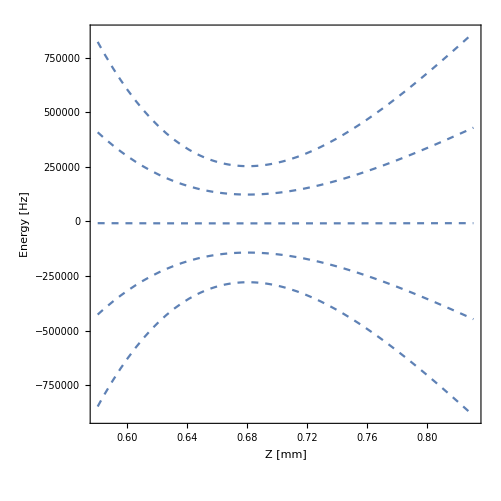

16 lines of corrupt data deleted.